```mathematica
SetDirectory["/Users/jogh/research/ExQuareum/repo/predictions/EQLab"];
<<EQLab2`

(*measurements*)
ProbabilityPlus=0.5;
UserMeasure[]:=RandomReal[]//Which[#<ProbabilityPlus,1,True,-1]&
(*forecasts*)
predictivepower2[xrandom_,meas_]:=Which[meas==1,1-xrandom^6,meas==-1,xrandom^6]
predictivepower1[xrandom_,meas_]:=Which[meas==1,1-xrandom^2,meas==-1,xrandom^2]
predictivepower0[xrandom_,meas_]:=Which[meas==1,1-xrandom,meas==-1,xrandom]
predictivepowerm1[xrandom_,meas_]:=Which[meas==1,xrandom^(7/6) ,meas==-1,1-xrandom^(7/6) ]
predictivepowerm2[xrandom_,meas_]:=Which[meas==1,xrandom^(3/2) ,meas==-1,1-xrandom^(3/2) ]

predictivepower[xrandom_,meas_,g_]:=Which[
g==2,predictivepower2[xrandom,meas],
g==1,predictivepower1[xrandom,meas],
g==0,predictivepower0[xrandom,meas],
g==-1,predictivepowerm1[xrandom,meas],
g==-2,predictivepowerm2[xrandom,meas]
]

beliefinα={
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2    (*player E*)
};

probchangebeliefinα={
0.3,  (*player A*)
0.3,  (*player B*)
0.3,   (*player C*)
0.3,(*player D*)
0.3 (*player E*)
};

 PredictivePower=<|
"A"->(predictivepower[#1,#2,beliefinα[[1]]]&),
"B"->(predictivepower[#1,#2,beliefinα[[2]]]&),
"C"->(predictivepower[#1,#2,beliefinα[[3]]]&),
"D"->(predictivepower[#1,#2,beliefinα[[4]]]&),
"E"->(predictivepower[#1,#2,beliefinα[[5]]]&)
|>;
 
npredictors=PredictivePower//Length;
nquestions=1000;

BadRewardDifference=400;
BeliefCurrent={};
BELIEF={};
UpdateBelieveinαORIGINAL[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,changebelief={}},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

changebelief=Table[
TrueQ[avgrewards-rewards[[i]]> BadRewardDifference]&&(Random[]<probchangebeliefinα[[i]])
,{i,1,beliefinα//Length}];

beliefinα=Table[
Which[
changebelief[[i]]&&(beliefinα[[i]]>beliefinα[[leadingexpert]]),beliefinα[[i]]-1,
changebelief[[i]]&&(beliefinα[[i]]<beliefinα[[leadingexpert]]),beliefinα[[i]]+1,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];
AppendTo[BeliefCurrent,beliefinα];
]

UpdateBelieveinαNEW[]:=Module[
{rewards,maxreward,avgrewards,leadingexpert,changebelief={}},
rewards=CREWARD[[-1,All,-1]];
maxreward=Max[rewards];
avgrewards=Mean[rewards];
leadingexpert=Position[rewards,maxreward]//Flatten//Part[#,1]&;

changebelief=Table[
TrueQ[rewards[[leadingexpert]]-rewards[[i]]> BadRewardDifference]&&(Random[]<probchangebeliefinα[[i]])
,{i,1,beliefinα//Length}];

beliefinα=Table[
Which[
changebelief[[i]]&&(beliefinα[[i]]>beliefinα[[leadingexpert]]),beliefinα[[i]]-1,
changebelief[[i]]&&(beliefinα[[i]]<beliefinα[[leadingexpert]]),beliefinα[[i]]+1,
True,beliefinα[[i]]
],
{i,1,beliefinα//Length}
];
AppendTo[BeliefCurrent,beliefinα];
]
UpdateBelieveinα=UpdateBelieveinαORIGINAL;

PrintBelieveinα[]:=Module[
{names=PLOTLEGENDS[[1,1;;npredictors]],output},
output=Table[names[[i]]<>"->"<>ToString[beliefinα[[i]]]<>"\n",{i,1,npredictors}]//StringJoin;
Print[Style["------ Current belief in theory α ---------",Red,Large]];
Print[Style[output,Blue,Large]]
]


UserPredict[exp_,newquestion_]:=Module[
{forecasts={}},
Which[
(exp//Length)>0,UpdateBelieveinα[];,
True,Nothing
];
forecasts=Table[RandomReal[{0.001,0.999}]//PredictivePower[i][#,newquestion[[2]]]&,{i,{"A","B","C","D","E"}}];
forecasts
]


(*resolutions*)
Bias={
0.3,(*"A"*)
0.3,(*"B"*)
0.3,(*"C"*)
0.3,(*"D"*)
0.3    (*"E"*)
};
thresholdprobplus=0.9;
thresholdprobminus[]:=1-thresholdprobplus;
UserResolve[exp_,newquestion_]:=Table[RandomReal[]//Which[#<Bias[[i]]&&newquestion[[2]]==1&&newquestion[[1,i]]<thresholdprobminus[],-1,#<Bias[[i]]&&newquestion[[2]]==-1&&newquestion[[1,i]]>thresholdprobplus,1,True,newquestion[[2]]]&,{i,{1,2,3,4,5}}]

(*condition to stop simulation*)
UserStop[]:=(beliefinα//DeleteDuplicates//Length)==1;

(*load user function into EQLab*)
SetUserFunctions[]
nquestions=5000;
UpdateBelieveinα=UpdateBelieveinαORIGINAL;

initsimulation[]:=Module[
{},
beliefinα={
2,  (*player A*)
1,  (*player B*)
0,   (*player C*)
-1,(*player D*)
-2    (*player E*)
};
BeliefCurrent={};
]

outputsimulation[]:=Module[
{},
AppendTo[BELIEF,BeliefCurrent];
PrintBelieveinα[];
markerlist=marker2[White,#1,#2]&@@@(ColorData[97,"ColorList"]//Table[{#[[i]],50-i*7},{i,1,npredictors}]&);
plotbelief=BELIEF[[-1,All]]//Transpose//ListLinePlot[#,PlotMarkers->markerlist,PlotRange->{-2.5,2.5},ImageSize->{1000,500},LabelStyle->Directive[Bold, 16],AxesOrigin->{-(Length[#[[1]]]*0.05),-0.5},AxesLabel->{Style["j",Bold,Large],Style["α",Bold,Large]},PlotLegends->PLOTLEGENDS,PlotStyle->Thick]&;
Print[plotbelief];

]
```

Ted, run this

------ Current belief in theory α ---------

expert A->2
expert B->2
expert C->2
expert D->2
expert E->2

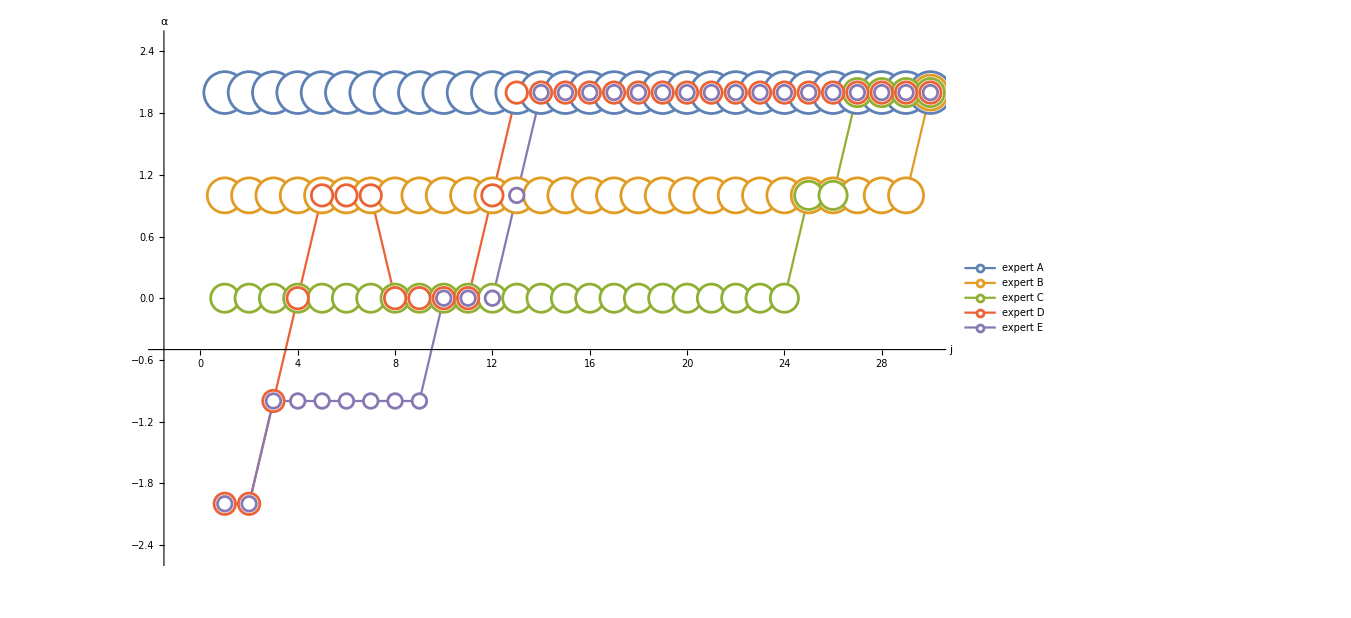

-Graphics-

-Graphics-

```mathematica
BadRewardDifference=0.01;
nquestions=20000;
thresholdprobplus=0.9;
Bias={
0.0,(*"A"*)
0.0,(*"B"*)
0.0,(*"C"*)
0.0,(*"D"*)
0.0  (*"E"*)
};
probchangebeliefinα={
0.5,  (*player A*)
0.5,  (*player B*)
0.5,   (*player C*)
0.5,(*player D*)
0.5(*player E*)
};
initsimulation[]
RunExperimentStop[]
outputsimulation[]
ShowPlots[-1,"rcumul"]
ShowPlots[-1,"savgj"]
```